# Anomaly cancellation

Generation-independent charges

## Equations for cancellation of anomalies

### [SU(3)]^2×(U(1))_X, [SU(2)]^2×(U(1))_X, [(U(1))_Y]^2×(U(1))_X

In addition to the linear anomaly cancellation condition we impose the proper Yukawa for the charged leptons in order to involve h in the calculations, because some references uses h as a free parameter. H have Y=1/2:

(e_R)^*L·H̃

```mathematica
xx=Solve[{u+d-2q==0,l==-3q,6e+8u+2d-3l-q==0,l-h-e==0},{h,q,u,d}]
```

{{h→-e+l,q→-l/3,u→-e+(2 l)/3,d→1/3 (3 e-4 l)}}

```mathematica
xx[[1]]
```

{h→-e+l,q→-l/3,u→-e+(2 l)/3,d→1/3 (3 e-4 l)}

### [(U(1))_X]^2×(U(1))_Y

The quadratic expansion is not independent

```mathematica
Simplify[ Expand[(-e^2+2 u^2-d^2+l^2-q^2)/.xx[[1]]] ]
```

0

### [(U(1))_X]^3

```mathematica
cc=Simplify[Expand[(e^3+3 u^3+3 d^3-2 l^3-6 q^3)/.xx[[1]]]]
```

(e-2 l)^3

### [Grav]^2×(U(1))_X

Mixed gauge  gravitational anomaly

```mathematica
rr=Simplify[{e+u+d-2l-2q}/.xx[[1]]]
```

{e-2 l}

## Other Yukawas

The model predicts a single Higgs for the Yukawas of the charged fermion

(d_R)^*Q·H̃+(u_R)^*Q·H

h_2  X-charges

```mathematica
Simplify[{q-d-h,q-u+h}/.xx[[1]]]
```

{0,0}

## (U(1))_X for N_G generations

we define sumnα=∑n_α, sumn3α=∑n_α^3

```mathematica
Subscript[N, G]=3
```

3

```mathematica
cc=Subscript[N, G] rr+sumn3α
```

{3 (e-2 l)+sumn3α}

```mathematica
ccc=Solve[cc==0,sumn3α]
```

{{sumn3α→-3 (e-2 l)}}

```mathematica
rrr=Subscript[N, G] rr+sumnα
```

{3 (e-2 l)+sumnα}

```mathematica
rrr=Solve[rrr==0,sumnα]
```

{{sumnα→-3 (e-2 l)}}

```mathematica
rsol=Solve[(sumnα/.rrr[[1]])==-Subscript[N, G]r,e]
```

{{e→2 l+r}}

### Normalization

By defining

r=e-2l

It is possible always to that the solution for the charged fermion fields is invariant under the changes f→ f'=f/r

```mathematica
xxr=Solve[{u/r+d/r-2q/r==0,l/r==-3q/r,6e/r+8u/r+2d/r-3l/r-q/r==0,l/r-h/r-e/r==0},{h,q,u,d}]
```

{{h→-e+l,q→-l/3,u→1/3 (-3 e+2 l),d→1/3 (3 e-4 l)}}

```mathematica
Print["∑n_α^3=",-Subscript[N, G]Simplify[Expand[((e/r)^3+3(u/r)^3+3(d/r)^3-2(l/r)^3-6(q/r)^3)/.xxr[[1]]]]/.rsol[[1]]]
```

∑n_α^3=-3

```mathematica
Print["∑n_α=",-Subscript[N, G]Simplify[{e/r+u/r+d/r-2l/r-2q/r}/.xx[[1]]]/.rsol[[1]]]
```

∑n_α={-3}

### Solution in terms of one parameter

without lost of generality we can choose r=1

```mathematica
xx
```

{{h→-e+l,q→-l/3,u→-e+(2 l)/3,d→1/3 (3 e-4 l)}}

```mathematica
rsol
```

{{e→2 l+r}}

```mathematica
xxr1=Simplify[xx[[1]]/.(rsol/.r->1)]
```

{{h→-1-l,q→-l/3,u→-1-(4 l)/3,d→1+(2 l)/3}}

```mathematica
xsol=Join[(rsol/.r->1)[[1]],xxr1[[1]]]
```

{e→1+2 l,h→-1-l,q→-l/3,u→-1-(4 l)/3,d→1+(2 l)/3}

### Checks

```mathematica
rr/.xsol
```

{1}

```mathematica
cc/.xsol
```

{3+sumn3α}

## Applications

### Xenonphobic dark matter

In conclusion (U(1))_X, is not anomaly free,

General solution

by using the condition ∑n_α=-3 and ∑n_α^3=-3  we can eliminate an additional X-charge that we choose to be

```mathematica
fu=u+q;
fd=d+q;
```

```mathematica
fn=fu+2fd;
fp=2fu+fd;
```

```mathematica
ff=Simplify[(fn/fp)/.xsol]
```

(-1+l)/(1+3 l)

```mathematica
f[a_,b_]:=Module[{},
ll=Solve[ff==a/b,l];
Join[ll[[1]],xsol/.ll[[1]]]]
```

#### -5/7

```mathematica
f[-5,7]
```

{l→1/11,e→13/11,h→-12/11,q→-1/33,u→-37/33,d→35/33}

#### -6/10

```mathematica
f[-6,10]
```

{l→1/7,e→9/7,h→-8/7,q→-1/21,u→-25/21,d→23/21}

#### -3/4

```mathematica
f[-3,4]
```

{l→1/13,e→15/13,h→-14/13,q→-1/39,u→-43/39,d→41/39}

#### -7/10

```mathematica
f[-7,10]
```

{l→3/31,e→37/31,h→-34/31,q→-1/31,u→-35/31,d→33/31}

```mathematica
bs=f[-7,11]
```

{l→1/8,e→5/4,h→-9/8,q→-1/24,u→-7/6,d→13/12}

```mathematica
X={l,e,h,q,u,d}
```

{l,e,h,q,u,d}

```mathematica
XX=ConstantArray[0,6];
Do[XX[[i]]=(X[[i]]/.bs[[i]])*4,{i,1,6}]
```

```mathematica
XX
```

{1/2,5,-9/2,-1/6,-14/3,13/3}

{0,0,0,0,0,0}

```mathematica
XX[1
```

XX

```mathematica
l/.l->1/8
```

1/8

```mathematica
Do[If[a/b≥ -0.8 && a/b≤-0.6&&Denominator[a/b]==b,Print[a,"/",b,":",f[a,b],N[a/b]]];
,{a,-50,-1},{b,1,30}]
```

-23/29:{l→3/49,e→55/49,h→-52/49,q→-1/49,u→-53/49,d→51/49}-0.793103

-23/30:{l→7/99,e→113/99,h→-106/99,q→-7/297,u→-325/297,d→311/297}-0.766667

-22/29:{l→7/95,e→109/95,h→-102/95,q→-7/285,u→-313/285,d→299/285}-0.758621

-21/29:{l→2/23,e→27/23,h→-25/23,q→-2/69,u→-77/69,d→73/69}-0.724138

-20/27:{l→7/87,e→101/87,h→-94/87,q→-7/261,u→-289/261,d→275/261}-0.740741

-20/29:{l→9/89,e→107/89,h→-98/89,q→-3/89,u→-101/89,d→95/89}-0.689655

-19/24:{l→5/81,e→91/81,h→-86/81,q→-5/243,u→-263/243,d→253/243}-0.791667

-19/25:{l→3/41,e→47/41,h→-44/41,q→-1/41,u→-45/41,d→43/41}-0.76

-19/26:{l→7/83,e→97/83,h→-90/83,q→-7/249,u→-277/249,d→263/249}-0.730769

-19/27:{l→2/21,e→25/21,h→-23/21,q→-2/63,u→-71/63,d→67/63}-0.703704

-19/28:{l→9/85,e→103/85,h→-94/85,q→-3/85,u→-97/85,d→91/85}-0.678571

-19/29:{l→5/43,e→53/43,h→-48/43,q→-5/129,u→-149/129,d→139/129}-0.655172

-19/30:{l→11/87,e→109/87,h→-98/87,q→-11/261,u→-305/261,d→283/261}-0.633333

-18/23:{l→5/77,e→87/77,h→-82/77,q→-5/231,u→-251/231,d→241/231}-0.782609

-18/25:{l→7/79,e→93/79,h→-86/79,q→-7/237,u→-265/237,d→251/237}-0.72

-18/29:{l→11/83,e→105/83,h→-94/83,q→-11/249,u→-293/249,d→271/249}-0.62069

-17/22:{l→5/73,e→83/73,h→-78/73,q→-5/219,u→-239/219,d→229/219}-0.772727

-17/23:{l→3/37,e→43/37,h→-40/37,q→-1/37,u→-41/37,d→39/37}-0.73913

-17/24:{l→7/75,e→89/75,h→-82/75,q→-7/225,u→-253/225,d→239/225}-0.708333

-17/25:{l→2/19,e→23/19,h→-21/19,q→-2/57,u→-65/57,d→61/57}-0.68

-17/26:{l→9/77,e→95/77,h→-86/77,q→-3/77,u→-89/77,d→83/77}-0.653846

-17/27:{l→5/39,e→49/39,h→-44/39,q→-5/117,u→-137/117,d→127/117}-0.62963

-17/28:{l→11/79,e→101/79,h→-90/79,q→-11/237,u→-281/237,d→259/237}-0.607143

-16/21:{l→5/69,e→79/69,h→-74/69,q→-5/207,u→-227/207,d→217/207}-0.761905

-16/23:{l→7/71,e→85/71,h→-78/71,q→-7/213,u→-241/213,d→227/213}-0.695652

-16/25:{l→9/73,e→91/73,h→-82/73,q→-3/73,u→-85/73,d→79/73}-0.64

-15/19:{l→1/16,e→9/8,h→-17/16,q→-1/48,u→-13/12,d→25/24}-0.789474

-15/22:{l→7/67,e→81/67,h→-74/67,q→-7/201,u→-229/201,d→215/201}-0.681818

-15/23:{l→2/17,e→21/17,h→-19/17,q→-2/51,u→-59/51,d→55/51}-0.652174

-14/19:{l→5/61,e→71/61,h→-66/61,q→-5/183,u→-203/183,d→193/183}-0.736842

-14/23:{l→9/65,e→83/65,h→-74/65,q→-3/65,u→-77/65,d→71/65}-0.608696

-13/17:{l→1/14,e→8/7,h→-15/14,q→-1/42,u→-23/21,d→22/21}-0.764706

-13/18:{l→5/57,e→67/57,h→-62/57,q→-5/171,u→-191/171,d→181/171}-0.722222

-13/19:{l→3/29,e→35/29,h→-32/29,q→-1/29,u→-33/29,d→31/29}-0.684211

-13/20:{l→7/59,e→73/59,h→-66/59,q→-7/177,u→-205/177,d→191/177}-0.65

-13/21:{l→2/15,e→19/15,h→-17/15,q→-2/45,u→-53/45,d→49/45}-0.619048

-12/17:{l→5/53,e→63/53,h→-58/53,q→-5/159,u→-179/159,d→169/159}-0.705882

-12/19:{l→7/55,e→69/55,h→-62/55,q→-7/165,u→-193/165,d→179/165}-0.631579

-11/14:{l→3/47,e→53/47,h→-50/47,q→-1/47,u→-51/47,d→49/47}-0.785714

-11/15:{l→1/12,e→7/6,h→-13/12,q→-1/36,u→-10/9,d→19/18}-0.733333

-11/16:{l→5/49,e→59/49,h→-54/49,q→-5/147,u→-167/147,d→157/147}-0.6875

-11/17:{l→3/25,e→31/25,h→-28/25,q→-1/25,u→-29/25,d→27/25}-0.647059

-11/18:{l→7/51,e→65/51,h→-58/51,q→-7/153,u→-181/153,d→167/153}-0.611111

-10/13:{l→3/43,e→49/43,h→-46/43,q→-1/43,u→-47/43,d→45/43}-0.769231

-9/13:{l→1/10,e→6/5,h→-11/10,q→-1/30,u→-17/15,d→16/15}-0.692308

-9/14:{l→5/41,e→51/41,h→-46/41,q→-5/123,u→-143/123,d→133/123}-0.642857

-8/11:{l→3/35,e→41/35,h→-38/35,q→-1/35,u→-39/35,d→37/35}-0.727273

-8/13:{l→5/37,e→47/37,h→-42/37,q→-5/111,u→-131/111,d→121/111}-0.615385

-7/9:{l→1/15,e→17/15,h→-16/15,q→-1/45,u→-49/45,d→47/45}-0.777778

-7/10:{l→3/31,e→37/31,h→-34/31,q→-1/31,u→-35/31,d→33/31}-0.7

-7/11:{l→1/8,e→5/4,h→-9/8,q→-1/24,u→-7/6,d→13/12}-0.636364

-5/7:{l→1/11,e→13/11,h→-12/11,q→-1/33,u→-37/33,d→35/33}-0.714286

-5/8:{l→3/23,e→29/23,h→-26/23,q→-1/23,u→-27/23,d→25/23}-0.625

-4/5:{l→1/17,e→19/17,h→-18/17,q→-1/51,u→-55/51,d→53/51}-0.8

-3/4:{l→1/13,e→15/13,h→-14/13,q→-1/39,u→-43/39,d→41/39}-0.75

-3/5:{l→1/7,e→9/7,h→-8/7,q→-1/21,u→-25/21,d→23/21}-0.6

-2/3:{l→1/9,e→11/9,h→-10/9,q→-1/27,u→-31/27,d→29/27}-0.666667

```mathematica
f[-5,7]
```

{l→1/11,e→13/11,h→-12/11,q→-1/33,u→-37/33,d→35/33}

{l→1/13,e→15/13,h→-14/13,q→-1/39,u→-43/39,d→41/39}

```mathematica
Do[a/b,
```

```mathematica
Join[ll[[1]],xsol/.ll[[1]]]
```

{l→1/7,e→9/7,h→-8/7,q→-1/21,u→-25/21,d→23/21}

```mathematica
nn=Solve[mx==-ν,ν]
```

{{ν→-e-6 q}}

```mathematica
xxx=Simplify[xx/.nn[[1]]]
```

{{l→-3 q,u→-e-2 q,d→e+4 q}}

```mathematica
uu=nn[[1]][[1]]
```

ν→-e-6 q

```mathematica
QQ=xxx[[1]][[3]]
```

d→e+4 q

```mathematica
hh/.nn[[1]]
```

-e-3 q

```mathematica
fu=u+q;
fd=d+q;
```

```mathematica
fn=fu+2fd;
fp=2fu+fd;
```

```mathematica
ff=Simplify[(fn/fp/.uu)/.QQ]
```

(2 e+11 q+u)/(e+7 q+2 u)

```mathematica
N[5/7]
```

0.714286

```mathematica
xxx/.d->0
```

{{l→-3 q,u→-e-2 q,0→e+4 q}}

```mathematica
uu/.d->0
```

ν→-e-6 q

```mathematica
hh/.uu/.d->0
```

-e-3 q

```mathematica
s1=Solve[ff==-5/7,d]
```

{}

```mathematica
s2=Solve[ff==-3/4,d]
```

{}

```mathematica
xxx/.s1
```

{{l→-3 q,u→-e-2 q,d→e+4 q}}

```mathematica
qqq
```

qqq

```mathematica
Solve[ff==6/10,d]
```

{}

```mathematica
1+1
```

2

```mathematica
xx
```

{{h→-e+l,q→-l/3,u→-e+(2 l)/3,d→1/3 (3 e-4 l)}}

```mathematica
xx/.{l->3,e->4}
```

{{h→-1,q→-1,u→-2,d→0}}

```mathematica
rr/.{l->3,e->4}
```

{-2}

```mathematica
cc/.{l->3,e->4}
```

-8

### ΔN_eff calculation

```mathematica
Subscript[N, c]=3;
Subscript[N, W]=2;
Subscript[s, L][x_]:=x;
Subscript[s, R][x_]:=x;
Subscript[μ, L][x_]:=x;
Subscript[μ, R][x_]:=x;
Subscript[ν, L2][x_]:=x;
Subscript[ν, L3][x_]:=x;
Nα={νL2->1,νL3->0};
DNeff=e^2+(Subscript[μ, R][e])^2+Subscript[N, W] l^2+(Subscript[μ, L][l])^2+(Subscript[ν, L2][l])^2+(Subscript[ν, L3][l])^2+Subscript[N, c] Subscript[N, W](q^2)+Subscript[N, c](d^2+u^2+(Subscript[s, L][q])^2+(Subscript[s, R][d])^2)
```

2 e^2+5 l^2+6 q^2+3 (2 d^2+q^2+u^2)

```mathematica
xx
```

{{h→-e+l,q→-l/3,u→-e+(2 l)/3,d→1/3 (3 e-4 l)}}

```mathematica
ΔNeff2=Simplify[DNeff/.xx[[1]]/.Nα]
```

11 e^2-20 e l+18 l^2

```mathematica
Plot3D[ΔNeff2,{l,-10,10},{e,-10,10}]
```

-Graphics3D-

67+20 x+14 x^2

```mathematica
Subscript[ΔN, eff][x_]:=(Simplify[DNeff/.xsol/.Nα])/.l->x
```

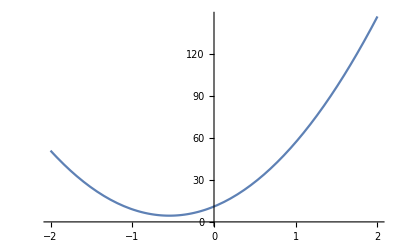

Plot

```mathematica
Plot[Subscript[ΔN, eff][l],{l,-2,2}]
Plot
```

```mathematica
lmin=Solve[D[Subscript[ΔN, eff][l],l]==0,l]
```

{{l→-6/11}}

```mathematica
Subscript[ΔN, eff][l]/.lmin[[1]]
N[Subscript[ΔN, eff][l]/.lmin[[1]]]
```

49/11

4.45455

4.45455

```mathematica
N[{Subscript[ΔN, eff][-1],Subscript[ΔN, eff][0],Subscript[ΔN, eff][-3/2],Subscript[ΔN, eff][-1/2]}]
```

{9.,11.,24.5,4.5}